```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

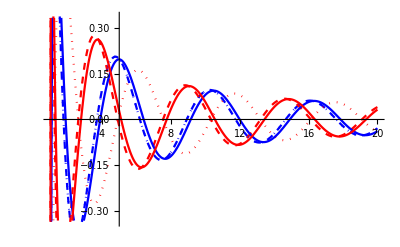

```mathematica
ϵ=10^-5;
Block[{ω,l,r∞,r0,R∞,Rp∞,ν,μ1,s,μ2},
ω=1;l=0;s=0;
r∞=20;r0=1+ϵ;
ν=0;μ1=0;μ2=-(s+1);
R∞=Exp[-I ω (r∞+Log[-1+r∞])]/(r∞);
Rp∞=(ⅇ^(-ⅈ ω (r∞+Log[-1+r∞])) (1+r∞ (-1-ⅈ r∞ ω)))/((-1+r∞) (r∞)^2);
solIn=NDSolve[{R''[r]+(1/r+1/(r-1))R'[r]+(r^3 ω^2-(r-1)l (l+1))/(r(r-1)^2)R[r]==0,R[r∞]==R∞,R'[r∞]==Rp∞},R,{r,r0,r∞},WorkingPrecision->30,AccuracyGoal->30];
p1=Plot[Evaluate[{Re[R[r]],Im[R[r]]}/.solIn],{r,r0,r∞},PlotStyle->{{Blue,Dashed},{Red,Dashed}}];
]
Block[{ω,l,r∞,r0,R∞,Rp∞,ν,μ1,s,μ2},
ω=1;l=0;s=0;
r∞=20;r0=1+ϵ;
ν=0;μ1=0;μ2=-(s+1);
R∞=Exp[I ω (r∞+Log[-1+r∞])]/(r∞);
Rp∞=(ⅇ^(ⅈ ω (r∞+Log[-1+r∞])) (1+r∞ (-1+ⅈ r∞ ω)))/((-1+r∞) (r∞)^2);
solOut=NDSolve[{R''[r]+(1/r+1/(r-1))R'[r]+(r^3 ω^2-(r-1)l (l+1))/(r(r-1)^2)R[r]==0,R[r∞]==R∞,R'[r∞]==Rp∞},R,{r,r0,r∞},WorkingPrecision->30,AccuracyGoal->30];
p2=Plot[Evaluate[{Re[R[r]],Im[R[r]]}/.solOut],{r,r0,r∞},PlotStyle->{{Blue,Dotted},{Red,Dotted}}];
]
Block[{ω,l,r∞,r0,R0,Rp0,ν,μ1,s,μ2},
ω=1;l=0;s=0;
r∞=20;r0=1+ϵ;
ν=0;μ1=0;μ2=-(s+1);
R0=Exp[-I ω (r0+Log[-1+r0])]/r0;
Rp0=(ⅇ^(-ⅈ ω (r0+Log[-1+r0])) (1+r0 (-1-ⅈ r0 ω)))/((-1+r0) r0^2);
solCausal=NDSolve[{R''[r]+(1/r+1/(r-1))R'[r]+(r^3 ω^2-(r-1)l (l+1))/(r(r-1)^2)R[r]==0,R[r0]==R0,R'[r0]==Rp0},R,{r,r0,r∞},WorkingPrecision->30,AccuracyGoal->30];
p3=Plot[Evaluate[{Re[R[r]],Im[R[r]]}/.solCausal],{r,r0,r∞},PlotStyle->{{Blue},{Red}}];
]
RIn[r_]:=Evaluate[R[r]/.solIn];
ROut[r_]:=Evaluate[R[r]/.solOut];
RCausal[r_]:=Evaluate[R[r]/.solCausal];
Show[p1,p2,p3,PlotRange->All]
rpts=Table[r,{r,10,20,1/2}];
Rpts=RCausal[#]&/@rpts//Flatten;
data={rpts,Rpts}//Transpose;
model=AIn RIn[r]+AOut ROut[r];
fit=FindFit[data,model,{AIn,AOut},r];
modelf=Function[{r},Evaluate[model/.fit]];
{RIn[r0],ROut[r0],RCausal[r0]}/.{r0->1+ϵ,r∞->20};
{RIn[r∞],ROut[r∞],RCausal[r∞],RIn'[r∞],ROut'[r∞],RCausal'[r∞]}/.{r0->1+ϵ,r∞->20};
Solve[{Rc∞==Ao Ro∞+Ai Ri∞,Rcp∞==Ao Rop∞+Ai Rip∞}//.{Ri∞->RIn[r∞],Ro∞->ROut[r∞],Rc∞->RCausal[r∞],Rip∞->RIn'[r∞],Rop∞->ROut'[r∞],Rcp∞->RCausal'[r∞],r0->1+ϵ,r∞->20},{Ai,Ao}];
Abs[AIn]^2/(Abs[AIn]^2+Abs[AOut]^2)/.fit;
{Abs[AOut/AIn]^2,1-Abs[AOut/AIn]^2}/.fit;
```

```mathematica
Solve[{Rc∞==Ao Ro∞+Ai Ri∞,Rcp∞==Ao Rop∞+Ai Rip∞},{Ai,Ao}]//FullSimplify
```

{{Ai→(Rc∞ Rop∞-Rcp∞ Ro∞)/(Ri∞ Rop∞-Rip∞ Ro∞),Ao→(Rc∞ Rip∞-Rcp∞ Ri∞)/(-Ri∞ Rop∞+Rip∞ Ro∞)}}

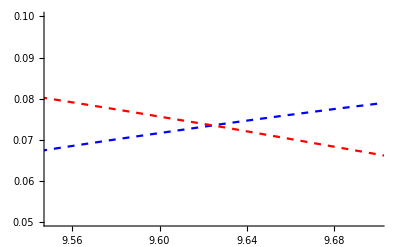

```mathematica
Show[p1,PlotRange->{{9.55,9.7},{0.05,0.1}}]
```